```mathematica
DSolve[u^4*D[psi[u],u,u]-a u^2 psi[u]+e psi[u]==0,psi[u],u]
```

{{psi[u]→2^(-1/2 √(1+4 a)+1/2 (1+√(1+4 a))) e^(1/4 √(1+4 a)+1/4 (-1-√(1+4 a))) (1/u)^(1/2 √(1+4 a)+1/2 (-1-√(1+4 a))) BesselJ[-1/2 √(1+4 a),(√e)/u] C[1] Gamma[1-1/2 √(1+4 a)]+2^(1/2 √(1+4 a)+1/2 (1-√(1+4 a))) e^(-1/4 √(1+4 a)+1/4 (-1+√(1+4 a))) (1/u)^(-1/2 √(1+4 a)+1/2 (-1+√(1+4 a))) BesselJ[1/2 √(1+4 a),(√e)/u] C[2] Gamma[1+1/2 √(1+4 a)]}}

```mathematica
e=5 10^-3
```

1/200

NDSolve::berr: There are significant errors {0.`, 1.0311281290441288`*^-7} in the boundary value residuals. Returning the best solution found.

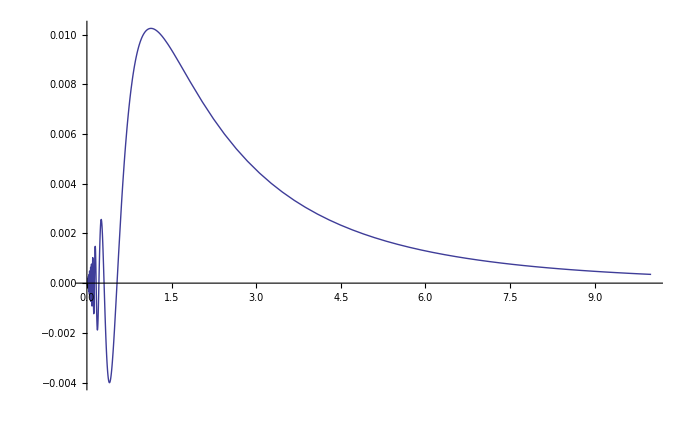

NDSolve::berr: There are significant errors {0.`, 1.0311281290441288`*^-7} in the boundary value residuals. Returning the best solution found.

NDSolve::berr: "
StyleBox[\"\\\"<There are significant errors >\\\"\", \"MT\"]
StyleBox[
RowBox[{\"{\", 
RowBox[{\"0.\", \",\", \"1.03113×10^-7\"1.03113*}], \"}\"}], \"MT\"]
StyleBox[\"\\\"< in the boundary value residuals. Returning the best solution found.>\\\"\", \"MT\"] (*ButtonBox[

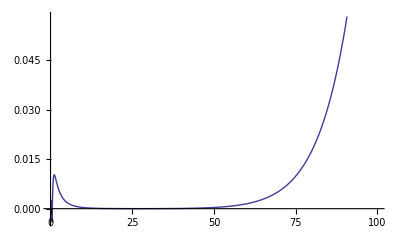

```mathematica
S=NDSolve[{u^4*D[psi[u],u,u]- u^3 psi[u]+ 4.999275psi[u]==0,psi[e]==0,psi[1]==0.01},psi[u],{u,e,10}];
Plot[S[[1,1,2]],{u,e,10}]
```